# Homework 21

## Problem 21.1

Note: You have already done a lot of the work for this problem back in HW #16 Written Problem #1. Go back and take a look at that if you would like!

A double pendulum (such as that illustrated in Figure 7.3 in the text) consists of two identical pendula attached one to the other. The upper pendulum is moved to an angle of 30 degrees and released from rest. Find the motion of the system. 

d = 1.00 m is the length of pendulum 
m = 250 g is the mass of each pendulum
theta1 is the angle (0 is down) of the upper pendulum,
theta2 is at the angle of the lower pendulum.

Note that you will get some long expressions in this problem.

```mathematica
Clear["'*"]
```

Write down expressions for x1, x2, y1, and y2 and their derivatives in terms of the variables defined above. Then write the kinetic and potential energies and the Lagrangian in terms of these quantities.

```mathematica
x1=d*Sin[theta1]
x2=d*Sin[theta2]+x1
y1=-d*Cos[theta1]
y2=-d*Cos[theta2] + y1
x1dot=d*Cos[theta1] *theta1dot
x2dot=d*Cos[theta2]*theta2dot + x1dot
y1dot=d*Sin[theta1]*theta1dot
y2dot=d*Sin[theta2]*theta2dot + y1dot
T=m*(x1dot^2 + y1dot^2)/2 + m*(x2dot^2 + y2dot^2)/2
U=m*g*(y1 + y2)
L=T-U
```

d Sin[theta1]

d Sin[theta1]+d Sin[theta2]

-d Cos[theta1]

-d Cos[theta1]-d Cos[theta2]

d theta1dot Cos[theta1]

d theta1dot Cos[theta1]+d theta2dot Cos[theta2]

d theta1dot Sin[theta1]

d theta1dot Sin[theta1]+d theta2dot Sin[theta2]

1/2 m (d^2 theta1dot^2 Cos[theta1]^2+d^2 theta1dot^2 Sin[theta1]^2)+1/2 m ((d theta1dot Cos[theta1]+d theta2dot Cos[theta2])^2+(d theta1dot Sin[theta1]+d theta2dot Sin[theta2])^2)

g m (-2 d Cos[theta1]-d Cos[theta2])

-g m (-2 d Cos[theta1]-d Cos[theta2])+1/2 m (d^2 theta1dot^2 Cos[theta1]^2+d^2 theta1dot^2 Sin[theta1]^2)+1/2 m ((d theta1dot Cos[theta1]+d theta2dot Cos[theta2])^2+(d theta1dot Sin[theta1]+d theta2dot Sin[theta2])^2)

### Solutions

```mathematica
x1$=d*Sin[theta1];
x2$=d*(Sin[theta1]+Sin[theta2]);
y1$=-d*Cos[theta1];
y2$=-d*(Cos[theta1]+Cos[theta2]);
x1dot$=d*Cos[theta1]*theta1dot;
x2dot$=d*(Cos[theta1]*theta1dot+Cos[theta2]*theta2dot);
y1dot$=d*Sin[theta1]*theta1dot;
y2dot$=d*(Sin[theta1]*theta1dot+Sin[theta2]*theta2dot);
T$=m/2*(x1dot^2+y1dot^2)+m/2*(x2dot^2+y2dot^2);
U$=m*g*(y1$+y2$)
If[FullSimplify[Solve[T==T$,m]=={{}}],Print["T is correct"],Print["T is incorrect"]]
If[FullSimplify[Solve[U==U$,m]=={{}}],Print["U is correct"],Print["U is incorrect"]]
```

g m (-d Cos[theta1]-d (Cos[theta1]+Cos[theta2]))

T is correct

U is correct

Now write equations for p1 and p2, the generalized momenta conjugate to theta1 and theta2.

```mathematica
eq1=p1==D[L, theta1dot]
eq2=p2==D[L, theta2dot]
```

p1==1/2 m (2 d^2 theta1dot Cos[theta1]^2+2 d^2 theta1dot Sin[theta1]^2)+1/2 m (2 d Cos[theta1] (d theta1dot Cos[theta1]+d theta2dot Cos[theta2])+2 d Sin[theta1] (d theta1dot Sin[theta1]+d theta2dot Sin[theta2]))

p2==1/2 m (2 d Cos[theta2] (d theta1dot Cos[theta1]+d theta2dot Cos[theta2])+2 d Sin[theta2] (d theta1dot Sin[theta1]+d theta2dot Sin[theta2]))

```mathematica
sols=Solve[{eq1,eq2},{theta1dot,theta2dot}];
theta1dot=theta1dot/.sols[[1]]
theta2dot=theta2dot/.sols[[1]]
T=FullSimplify[T]
```

-(p2 Cos[theta1] Cos[theta2]-p1 Cos[theta2]^2+p2 Sin[theta1] Sin[theta2]-p1 Sin[theta2]^2)/(d^2 m (Cos[theta1]^2 Cos[theta2]^2+2 Cos[theta2]^2 Sin[theta1]^2-2 Cos[theta1] Cos[theta2] Sin[theta1] Sin[theta2]+2 Cos[theta1]^2 Sin[theta2]^2+Sin[theta1]^2 Sin[theta2]^2))

-(-2 p2 Cos[theta1]^2+p1 Cos[theta1] Cos[theta2]-2 p2 Sin[theta1]^2+p1 Sin[theta1] Sin[theta2])/(d^2 m (Cos[theta1]^2 Cos[theta2]^2+2 Cos[theta2]^2 Sin[theta1]^2-2 Cos[theta1] Cos[theta2] Sin[theta1] Sin[theta2]+2 Cos[theta1]^2 Sin[theta2]^2+Sin[theta1]^2 Sin[theta2]^2))

-(p1^2+2 p2^2-2 p1 p2 Cos[theta1-theta2])/(d^2 m (-3+Cos[2 (theta1-theta2)]))

### Solution

```mathematica
T$=-(p1^2+2 p2^2-2 p1 p2 Cos[theta1-theta2])/(d^2 m (-3+Cos[2 (theta1-theta2)]));
If[FullSimplify[Solve[T==T$]]=={{}},Print["T is correct."],Print["T is incorrect."]]
```

T is correct.

Now form the Hamiltonian, take derivatives with respect to everything in sight, and construct the equations of motion. 

Note how complicated these equations are!

```mathematica
H=T+U;
dHd1=D[H,theta1]
dHdp1=D[H,p1]
dHd2=D[H,theta2]
dHdp2=D[H,p2]
```

2 d g m Sin[theta1]-(2 p1 p2 Sin[theta1-theta2])/(d^2 m (-3+Cos[2 (theta1-theta2)]))-(2 (p1^2+2 p2^2-2 p1 p2 Cos[theta1-theta2]) Sin[2 (theta1-theta2)])/(d^2 m (-3+Cos[2 (theta1-theta2)])^2)

-(2 p1-2 p2 Cos[theta1-theta2])/(d^2 m (-3+Cos[2 (theta1-theta2)]))

(2 p1 p2 Sin[theta1-theta2])/(d^2 m (-3+Cos[2 (theta1-theta2)]))+(2 (p1^2+2 p2^2-2 p1 p2 Cos[theta1-theta2]) Sin[2 (theta1-theta2)])/(d^2 m (-3+Cos[2 (theta1-theta2)])^2)+d g m Sin[theta2]

-(4 p2-2 p1 Cos[theta1-theta2])/(d^2 m (-3+Cos[2 (theta1-theta2)]))

```mathematica
rule={theta1->theta1[t],theta2->theta2[t],p1->p1[t],p2->p2[t],Dp1->p1'[t],Dp2->p2'[t],Dtheta1->theta1'[t],Dtheta2->theta2'[t]};
(*check the replacement rule in the preceding line to know what to use for the blanks below*)
eq1=-Dp1==dHd1/.rule
eqp1= Dtheta1==dHdp1/.rule
eq2=-Dp2==dHd2/.rule
eqp2=Dtheta2==dHdp2/.rule
```

-p1'[t]==2 d g m Sin[theta1[t]]-(2 p1[t] p2[t] Sin[theta1[t]-theta2[t]])/(d^2 m (-3+Cos[2 (theta1[t]-theta2[t])]))-(2 (p1[t]^2-2 Cos[theta1[t]-theta2[t]] p1[t] p2[t]+2 p2[t]^2) Sin[2 (theta1[t]-theta2[t])])/(d^2 m (-3+Cos[2 (theta1[t]-theta2[t])])^2)

theta1'[t]==-(2 p1[t]-2 Cos[theta1[t]-theta2[t]] p2[t])/(d^2 m (-3+Cos[2 (theta1[t]-theta2[t])]))

-p2'[t]==(2 p1[t] p2[t] Sin[theta1[t]-theta2[t]])/(d^2 m (-3+Cos[2 (theta1[t]-theta2[t])]))+(2 (p1[t]^2-2 Cos[theta1[t]-theta2[t]] p1[t] p2[t]+2 p2[t]^2) Sin[2 (theta1[t]-theta2[t])])/(d^2 m (-3+Cos[2 (theta1[t]-theta2[t])])^2)+d g m Sin[theta2[t]]

theta2'[t]==-(-2 Cos[theta1[t]-theta2[t]] p1[t]+4 p2[t])/(d^2 m (-3+Cos[2 (theta1[t]-theta2[t])]))

Finally, we put in numbers and solve the system numerically. Note the complex behavior.

{{theta1→InterpolatingFunction[…],theta2→InterpolatingFunction[…],p1→InterpolatingFunction[…],p2→InterpolatingFunction[…]}}

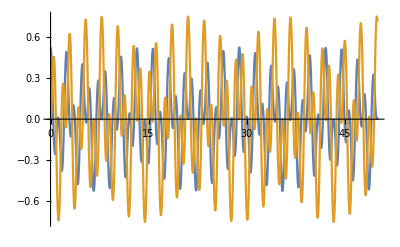

```mathematica
m=.250;
g=9.8;
d=1;
theta0=30*Pi/180;
sol1=NDSolve[{eq1,eqp1,eq2,eqp2,theta1[0]==theta0,theta2[0]==0,p1[0]==0,p2[0]==0},{theta1,theta2,p1,p2},{t,0,50}]
Plot[{Evaluate[theta1[t]/.sol1],Evaluate[theta2[t]/.sol1]},{t,0,50}]
```

## Problem 21.2

In this problem, we will generate phase space plots for a simple pendulum. I will go ahead and write down the Hamiltonian for you, but please make sure you can derive it on your own.

```mathematica
Quit[]
```

```mathematica
H=p^2/(2 m l^2)-m g l Cos[theta]
dHdp=D[H, p]
dHdtheta=-D[H, theta]
```

p^2/(2 l^2 m)-g l m Cos[theta]

p/(l^2 m)

-g l m Sin[theta]

```mathematica
rule={p->p[t],theta->theta[t],Dp->p'[t],Dtheta->theta'[t]};
eq1=-Dp ==dHdtheta/.rule
eq2=Dtheta==dHdp/.rule
```

-p'[t]==-g l m Sin[theta[t]]

theta'[t]==p[t]/(l^2 m)

Now generate phase-space plots for the following situations:
(1) A closed trajectory (i.e. oscillations back and forth)
(2) An open trajectory (i.e. the pendulum rotates continuously without turning around)
(3) The transition between closed and open

To do this, you will need to choose suitable initial conditions for each situation. For the transition trajectory, consider starting your pendulum out at something very close to vertically upward (say, 0.1 degree off the vertical).

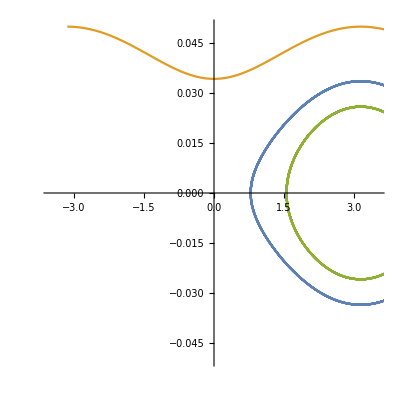

```mathematica
valsClosed={theta0->Pi/4,p0->0,m->0.1,l->0.15,g->9.8};
valsOpen={theta0->-Pi,p0->0.05,m->0.1,l->0.15,g->9.8};
valsTransition={theta0->89*Pi/180,p0->0,m->0.1,l->0.15,g->9.8};

tfinal=5;
sol1=NDSolve[{eq1,eq2,theta[0]==theta0,p[0]==p0}/.valsClosed,{theta,p},{t,0,tfinal}];
sol2=NDSolve[{eq1,eq2,theta[0]==theta0,p[0]==p0}/.valsOpen,{theta,p},{t,0,tfinal}];
sol3=NDSolve[{eq1,eq2,theta[0]==theta0,p[0]==p0}/.valsTransition,{theta,p},{t,0,tfinal}];

(* Hint: If you can't see the open trajectory, try using a smaller value for p0. Something smaller in magnitude than 0.03 should be fine.*)
ParametricPlot[Evaluate[{{theta[t],p[t]}/.sol1,{theta[t],p[t]}/.sol2,{theta[t],p[t]}/.sol3}],{t,0,tfinal},AspectRatio->1,PlotRange->{{-3.5,3.5},{-0.05,0.05}}]
```

## Written Problems

-Graphics-